Project 2 by Jieyu Ren (jxr477)

Note: both the code and the write-up are contained in this file.

Exercise 1.  Linear decision boundaries

a

data set of petal width and petal length of class 2

```mathematica
PL1={4.7,4.5,4.9,4,4.6,4.5,4.7,3.3,4.6,3.9,3.5,4.2,4,4.7,3.6,4.4,4.5,4.1,4.5,3.9,4.8,4,4.9,4.7,4.3,4.4,4.8,5,4.5,3.5,3.8,3.7,3.9,5.1,4.5,4.5,4.7,4.4,4.1,4,4.4,4.6,4,3.3,4.2,4.2,4.2,4.3,3,4.1};
```

```mathematica
PW1={1.4,1.5,1.5,1.3,1.5,1.3,1.6,1,1.3,1.4,1,1.5,1,1.4,1.3,1.4,1.5,1,1.5,1.1,1.8,1.3,1.5,1.2,1.3,1.4,1.4,1.7,1.5,1,1.1,1,1.2,1.6,1.5,1.6,1.5,1.3,1.3,1.3,1.2,1.4,1.2,1,1.3,1.2,1.3,1.3,1.1,1.3};
```

```mathematica
Length[PL1]
```

50

```mathematica
Length[PW1]
```

50

```mathematica
D1=Transpose@{PL1,PW1}
```

{{4.7,1.4},{4.5,1.5},{4.9,1.5},{4,1.3},{4.6,1.5},{4.5,1.3},{4.7,1.6},{3.3,1},{4.6,1.3},{3.9,1.4},{3.5,1},{4.2,1.5},{4,1},{4.7,1.4},{3.6,1.3},{4.4,1.4},{4.5,1.5},{4.1,1},{4.5,1.5},{3.9,1.1},{4.8,1.8},{4,1.3},{4.9,1.5},{4.7,1.2},{4.3,1.3},{4.4,1.4},{4.8,1.4},{5,1.7},{4.5,1.5},{3.5,1},{3.8,1.1},{3.7,1},{3.9,1.2},{5.1,1.6},{4.5,1.5},{4.5,1.6},{4.7,1.5},{4.4,1.3},{4.1,1.3},{4,1.3},{4.4,1.2},{4.6,1.4},{4,1.2},{3.3,1},{4.2,1.3},{4.2,1.2},{4.2,1.3},{4.3,1.3},{3,1.1},{4.1,1.3}}

plot of class 2

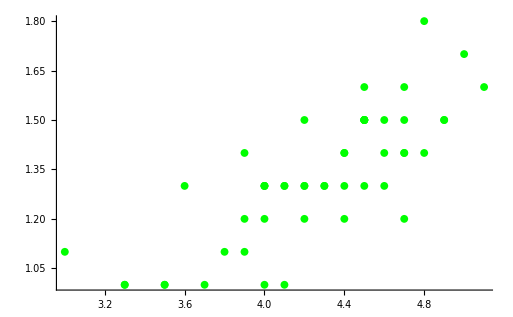

```mathematica
class2=ListPlot[D1,PlotStyle->Green]
```

```mathematica
PL2={6,5.1,5.9,5.6,5.8,6.6,4.5,6.3,5.8,6.1,5.1,5.3,5.5,5,5.1,5.3,5.5,6.7,6.9,5,5.7,4.9,6.7,4.9,5.7,6,4.8,4.9,5.6,5.8,6.1,6.4,5.6,5.1,5.6,6.1,5.6,5.5,4.8,5.4,5.6,5.1,5.1,5.9,5.7,5.2,5,5.2,5.4,5.1};
```

```mathematica
PW2={2.5,1.9,2.1,1.8,2.2,2.1,1.7,1.8,1.8,2.5,2,1.9,2.1,2,2.4,2.3,1.8,2.2,2.3,1.5,2.3,2,2,1.8,2.1,1.8,1.8,1.8,2.1,1.6,1.9,2,2.2,1.5,1.4,2.3,2.4,1.8,1.8,2.1,2.4,2.3,1.9,2.3,2.5,2.3,1.9,2,2.3,1.8};
```

```mathematica
Length[PL2]
```

50

```mathematica
Length[PW2]
```

50

```mathematica
D2=Transpose@{PL2,PW2}
```

{{6,2.5},{5.1,1.9},{5.9,2.1},{5.6,1.8},{5.8,2.2},{6.6,2.1},{4.5,1.7},{6.3,1.8},{5.8,1.8},{6.1,2.5},{5.1,2},{5.3,1.9},{5.5,2.1},{5,2},{5.1,2.4},{5.3,2.3},{5.5,1.8},{6.7,2.2},{6.9,2.3},{5,1.5},{5.7,2.3},{4.9,2},{6.7,2},{4.9,1.8},{5.7,2.1},{6,1.8},{4.8,1.8},{4.9,1.8},{5.6,2.1},{5.8,1.6},{6.1,1.9},{6.4,2},{5.6,2.2},{5.1,1.5},{5.6,1.4},{6.1,2.3},{5.6,2.4},{5.5,1.8},{4.8,1.8},{5.4,2.1},{5.6,2.4},{5.1,2.3},{5.1,1.9},{5.9,2.3},{5.7,2.5},{5.2,2.3},{5,1.9},{5.2,2},{5.4,2.3},{5.1,1.8}}

plot of class 3

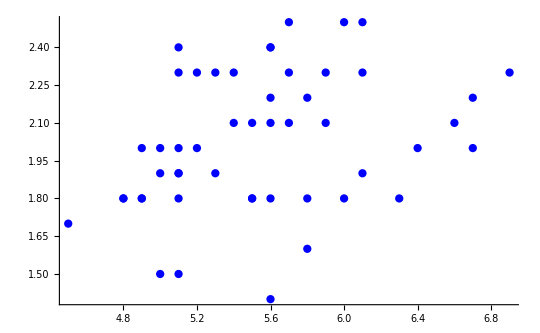

```mathematica
class3=ListPlot[D2,PlotStyle->Blue]
```

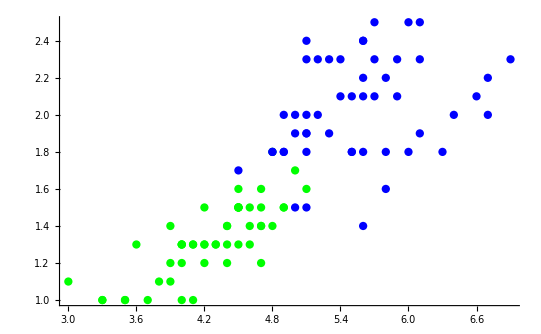

```mathematica
Show[class2,class3,PlotRange->All]
```

b

```mathematica
c=Classify[<|0->D1,1->D2|>,Method->"LogisticRegression"];
```

```mathematica
H=Join[D1,D2]
```

{{4.7,1.4},{4.5,1.5},{4.9,1.5},{4,1.3},{4.6,1.5},{4.5,1.3},{4.7,1.6},{3.3,1},{4.6,1.3},{3.9,1.4},{3.5,1},{4.2,1.5},{4,1},{4.7,1.4},{3.6,1.3},{4.4,1.4},{4.5,1.5},{4.1,1},{4.5,1.5},{3.9,1.1},{4.8,1.8},{4,1.3},{4.9,1.5},{4.7,1.2},{4.3,1.3},{4.4,1.4},{4.8,1.4},{5,1.7},{4.5,1.5},{3.5,1},{3.8,1.1},{3.7,1},{3.9,1.2},{5.1,1.6},{4.5,1.5},{4.5,1.6},{4.7,1.5},{4.4,1.3},{4.1,1.3},{4,1.3},{4.4,1.2},{4.6,1.4},{4,1.2},{3.3,1},{4.2,1.3},{4.2,1.2},{4.2,1.3},{4.3,1.3},{3,1.1},{4.1,1.3},{6,2.5},{5.1,1.9},{5.9,2.1},{5.6,1.8},{5.8,2.2},{6.6,2.1},{4.5,1.7},{6.3,1.8},{5.8,1.8},{6.1,2.5},{5.1,2},{5.3,1.9},{5.5,2.1},{5,2},{5.1,2.4},{5.3,2.3},{5.5,1.8},{6.7,2.2},{6.9,2.3},{5,1.5},{5.7,2.3},{4.9,2},{6.7,2},{4.9,1.8},{5.7,2.1},{6,1.8},{4.8,1.8},{4.9,1.8},{5.6,2.1},{5.8,1.6},{6.1,1.9},{6.4,2},{5.6,2.2},{5.1,1.5},{5.6,1.4},{6.1,2.3},{5.6,2.4},{5.5,1.8},{4.8,1.8},{5.4,2.1},{5.6,2.4},{5.1,2.3},{5.1,1.9},{5.9,2.3},{5.7,2.5},{5.2,2.3},{5,1.9},{5.2,2},{5.4,2.3},{5.1,1.8}}

```mathematica
P=Table[c[H[[i]]],{i,1,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

example outputs:

```mathematica
c[{6,2.5}]
```

1

```mathematica
c[{4.7,1.4}]
```

0

c

The decision boundary function with m1 and m2 equal to 1 and bias equal to -6.5:

```mathematica
F[x_]:=-x+6.5
```

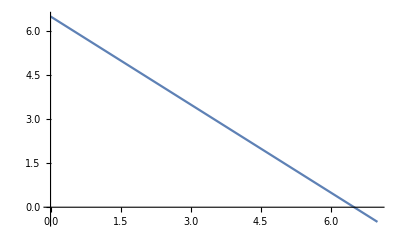

```mathematica
L=Plot[F[x],{x,0,7}]
```

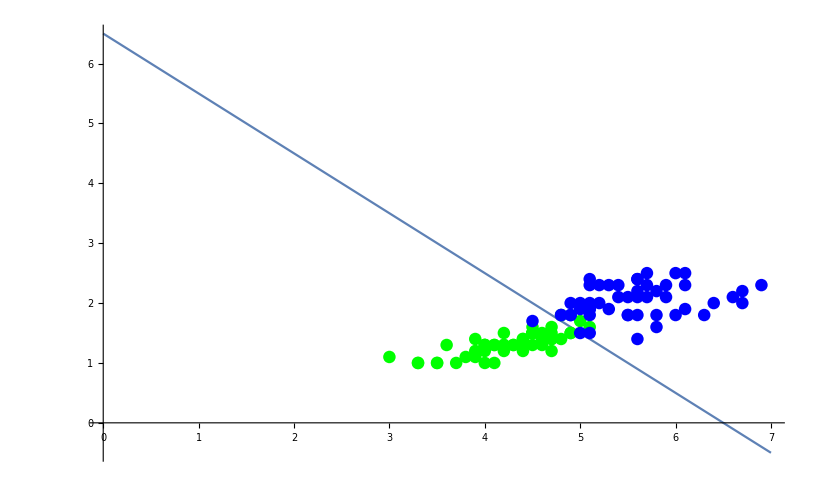

```mathematica
Show[L,class2,class3,PlotRange->All]
```

d

```mathematica
T=Table[{H[[i]],P[[i]]},{i,1,100}];
```

```mathematica
TT={{4.7,1.4,0},{4.5,1.5,0},{4.9,1.5,0},{4,1.3,0},{4.6,1.5,0},{4.5,1.3,0},{4.7,1.6,0},{3.3,1,0},{4.6,1.3,0},{3.9,1.4,0},{3.5,1,0},{4.2,1.5,0},{4,1,0},{4.7,1.4,0},{3.6,1.3,0},{4.4,1.4,0},{4.5,1.5,0},{4.1,1,0},{4.5,1.5,0},{3.9,1.1,0},{4.8,1.8,1},{4,1.3,0},{4.9,1.5,0},{4.7,1.2,0},{4.3,1.3,0},{4.4,1.4,0},{4.8,1.4,0},{5,1.7,1},{4.5,1.5,0},{3.5,1,0},{3.8,1.1,0},{3.7,1,0},{3.9,1.2,0},{5.1,1.6,1},{4.5,1.5,0},{4.5,1.6,0},{4.7,1.5,0},{4.4,1.3,0},{4.1,1.3,0},{4,1.3,0},{4.4,1.2,0},{4.6,1.4,0},{4,1.2,0},{3.3,1,0},{4.2,1.3,0},{4.2,1.2,0},{4.2,1.3,0},{4.3,1.3,0},{3,1.1,0},{4.1,1.3,0},{6,2.5,1},{5.1,1.9,1},{5.9,2.1,1},{5.6,1.8,1},{5.8,2.2,1},{6.6,2.1,1},{4.5,1.7,0},{6.3,1.8,1},{5.8,1.8,1},{6.1,2.5,1},{5.1,2,1},{5.3,1.9,1},{5.5,2.1,1},{5,2,1},{5.1,2.4,1},{5.3,2.3,1},{5.5,1.8,1},{6.7,2.2,1},{6.9,2.3,1},{5,1.5,0},{5.7,2.3,1},{4.9,2,1},{6.7,2,1},{4.9,1.8,1},{5.7,2.1,1},{6,1.8,1},{4.8,1.8,1},{4.9,1.8,1},{5.6,2.1,1},{5.8,1.6,1},{6.1,1.9,1},{6.4,2,1},{5.6,2.2,1},{5.1,1.5,0},{5.6,1.4,1},{6.1,2.3,1},{5.6,2.4,1},{5.5,1.8,1},{4.8,1.8,1},{5.4,2.1,1},{5.6,2.4,1},{5.1,2.3,1},{5.1,1.9,1},{5.9,2.3,1},{5.7,2.5,1},{5.2,2.3,1},{5,1.9,1},{5.2,2,1},{5.4,2.3,1},{5.1,1.8,1}};
```

```mathematica
Length[TT]
```

100

```mathematica
ListPlot3D[TT,AxesLabel->{"Pental Length","Pental Width","classifier output"}]
```

-Graphics3D-

e

example outputs:

```mathematica
c[{4.6,1.5}]
```

0

```mathematica
c[{4.8,1.4}]
```

0

```mathematica
c[{5.1,1.5}]
```

0

```mathematica
c[{5.1,1.6}]
```

1

```mathematica
c[{5.1,1.9}]
```

1

```mathematica
c[{4.8,1.8}]
```

1

Exercise 2. Neural networks

a

If the output is 0, the input vector is not in that class.

```mathematica
XX1[{x1_,x2_}]:=∑_(i=1)^50 If[{x1,x2}==D1[[i]],1,0]
```

```mathematica
XX2[{x1_,x2_}]:=∑_(i=1)^50 If[{x1,x2}==D2[[i]],1,0]
```

example outputs:

```mathematica
XX1[{4.7,1.4}]
```

2

```mathematica
XX2[{4.2,1.2}]
```

0

If the input vector is in class 2, output 0. Otherwise, output 1.

```mathematica
XXX1[{x1_,x2_}]:=If[XX1[{x1,x2}]==0,1,0]
```

```mathematica
XXX2[{x1_,x2_}]:=If[XX2[{x1,x2}]==0,0,1]
```

example outputs:

```mathematica
XXX1[{6,2.5}]
```

1

```mathematica
XXX2[{6,2.5}]
```

1

```mathematica
XXX1[{4.8,1.8}]
```

0

```mathematica
XXX2[{4.8,1.8}]
```

1

mean squared error function, XXX1[H[[n]]] and XXX2[H[[n]]] are the true class functions while c[H[[n]]] is the output of classifier.

```mathematica
MSE=1/100*(∑_(n=1)^50 (XXX1[H[[n]]]-c[H[[n]]])^2+∑_(n=51)^100 (XXX2[H[[n]]]-c[H[[n]]])^2)
```

3/50

```mathematica
N[MSE]
```

0.06

b

The first decision boundary (w1 = 1, w2 = 1, w0  = -6.5)

```mathematica
YY1[{x1_,x2_}]:=If[F[x1]<x2,1,0]
```

```mathematica
MSE1=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-YY1[H[[n]]])^2
```

7/100

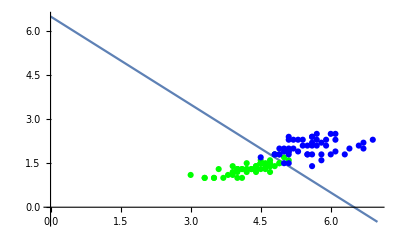

```mathematica
Show[L,class2,class3,PlotRange->All]
```

The second decision boundary (w1 = 1, w2 = 2, w0 = -10)

```mathematica
FF[x_]:=-1/2*x+5
```

```mathematica
YY2[{x1_,x2_}]:=If[FF[x1]<x2,1,0]
```

```mathematica
MSE2=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-YY2[H[[n]]])^2
```

33/100

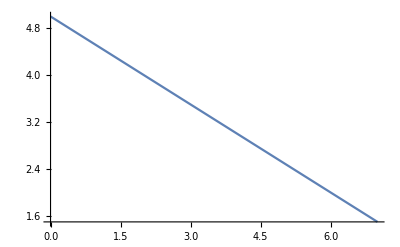

```mathematica
LL=Plot[FF[x],{x,0,7}]
```

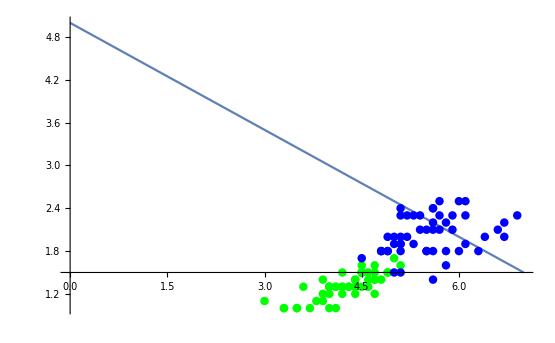

```mathematica
Show[LL,class2,class3,PlotRange->All]
```

c

Derivation of the gradient

(∂E)/w = 2/N(∑_(n=1)^N (_w T* x_n - c_n) * x_n)

d

vector form:

(∂E)/w = 2/N(∑_(n=1)^N (_w T* x_n - c_n) * x_n)

scalar form:

(∂E)/w_i = 2/N(∑_(n=1)^N (w_0 * x_(0,n) + ... + w_i*x_(i,n) - c_n) * x_(i,n))

e

```mathematica
G0[w0_]:=1/50∑_(n=1)^100 (w0- XXX1[H[[n]]])
```

```mathematica
G1[w0_,w1_,x1_]:=1/50∑_(n=1)^100 (w0 + w1*x1- XXX1[H[[n]]])*x1
```

```mathematica
G2[w0_,w1_,w2_,x1_,x2_]:=1/50∑_(n=1)^100 (w0 + w1*x1 +w2*x2- XXX1[H[[n]]])*x2
```

example: w1 = w2 = 1, w0 = -6.4, x1 = x2 = 2

```mathematica
G0[-6.4]
```

-13.76

```mathematica
G1[-6.4,1,2]
```

-19.52

```mathematica
G2[-6.4,1,1,2,2]
```

-11.52

```mathematica
FY0[x_]:=-x+6.4
```

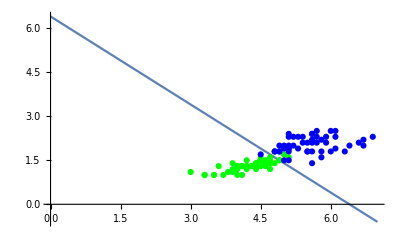

```mathematica
Show[Plot[FY0[x],{x,0,7},PlotRange->All],class2,class3,PlotRange->All]
```

change w0 to -6.5

```mathematica
G0[-6.5]
```

-13.96

```mathematica
G1[-6.5,1,2]
```

-19.92

```mathematica
G2[-6.5,1,1,2,2]
```

-11.92

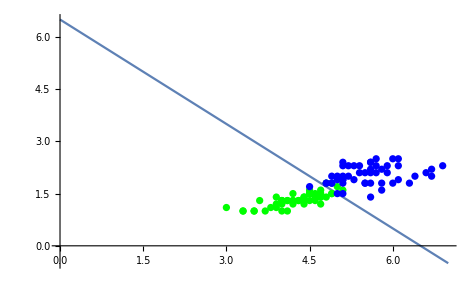

```mathematica
Show[L,class2,class3,PlotRange->All]
```

Exercise 3. Learning a decision boundary through optimization

a

start from w0 = -8, w1 = w2 =  1, assume x1 = x2 = 2, Epsilon = 0.08/100

```mathematica
Eps=0.08/100
```

0.0008

iteration 1

```mathematica
w01=-8-Eps *G0[-8]
```

-7.98643

```mathematica
w11=1-Eps*G1[-8,1,2]
```

1.02074

```mathematica
w21=1-Eps*G2[-8,1,1,2,2]
```

1.01434

```mathematica
FY1[x_]:=-(w11*x+w01)/w21
```

```mathematica
FFY1[{x1_,x2_}]:=If[FY1[x1]<x2,1,0]
```

b

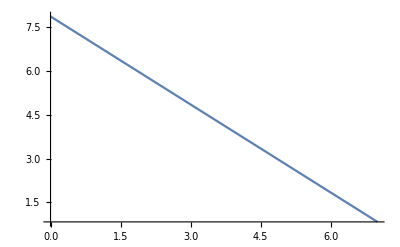

```mathematica
PY1=Plot[FY1[x],{x,0,7},PlotRange->All]
```

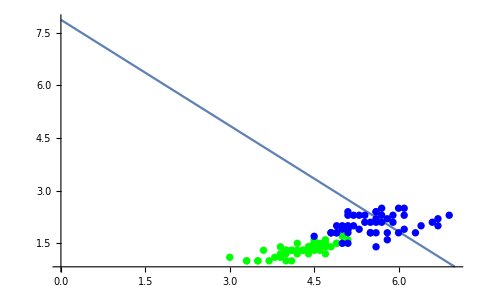

```mathematica
Show[PY1,class2,class3,PlotRange->All]
```

```mathematica
MSE3=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY1[H[[n]]])^2
```

31/100

```mathematica
LC1={MSE3};
```

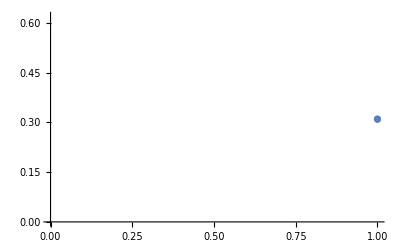

```mathematica
ListPlot[LC1]
```

c

iteration 2

```mathematica
w02=w01-Eps *G0[w01]
```

-7.97289

```mathematica
w12=w11-Eps*G1[w01,w11,2]
```

1.0413

```mathematica
w22=w21-Eps*G2[w01,w11,w21,2,2]
```

1.0284

```mathematica
FY2[x_]:=-(w12*x+w02)/w22
```

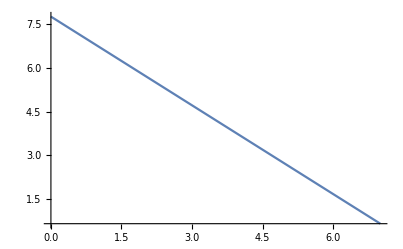

```mathematica
PY2=Plot[FY2[x],{x,0,7},PlotRange->All]
```

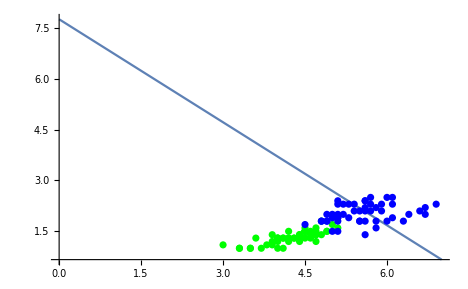

```mathematica
Show[PY2,class2,class3,PlotRange->All]
```

```mathematica
FFY2[{x1_,x2_}]:=If[FY2[x1]<x2,1,0]
```

```mathematica
MSE4=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY2[H[[n]]])^2
```

13/50

```mathematica
LC2={MSE3,MSE4};
```

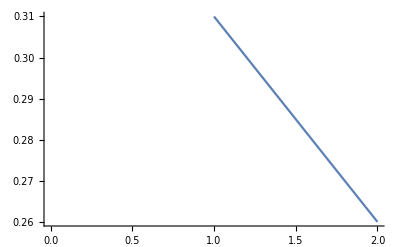

```mathematica
ListLinePlot[LC2]
```

iteration 3

```mathematica
w03=w02-Eps *G0[w02]
```

-7.95936

```mathematica
w13=w12-Eps*G1[w02,w12,2]
```

1.06168

```mathematica
w23=w22-Eps*G2[w02,w12,w22,2,2]
```

1.04221

```mathematica
FY3[x_]:=-(w13*x+w03)/w23
```

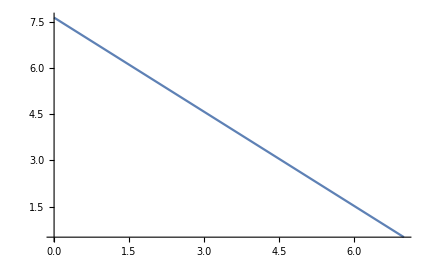

```mathematica
PY3=Plot[FY3[x],{x,0,7},PlotRange->All]
```

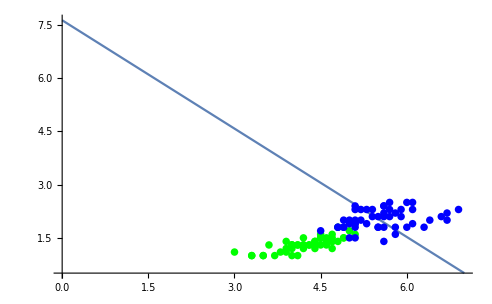

```mathematica
Show[PY3,class2,class3,PlotRange->All]
```

```mathematica
FFY3[{x1_,x2_}]:=If[FY3[x1]<x2,1,0]
```

```mathematica
MSE5=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY3[H[[n]]])^2
```

23/100

```mathematica
LC3={MSE3,MSE4,MSE5};
```

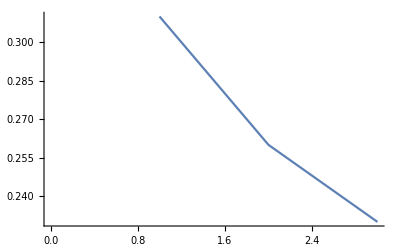

```mathematica
ListLinePlot[LC3]
```

iteration 4

```mathematica
w04=w03-Eps *G0[w03]
```

-7.94586

```mathematica
w14=w13-Eps*G1[w03,w13,2]
```

1.08189

```mathematica
w24=w23-Eps*G2[w03,w13,w23,2,2]
```

1.05575

```mathematica
FY4[x_]:=-(w14*x+w04)/w24
```

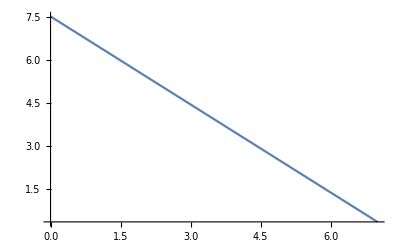

```mathematica
PY4=Plot[FY4[x],{x,0,7},PlotRange->All]
```

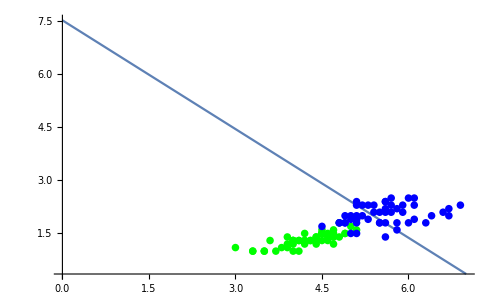

```mathematica
Show[PY4,class2,class3,PlotRange->All]
```

```mathematica
FFY4[{x1_,x2_}]:=If[FY4[x1]<x2,1,0]
```

```mathematica
MSE6=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY4[H[[n]]])^2
```

17/100

```mathematica
LC4={MSE3,MSE4,MSE5,MSE6};
```

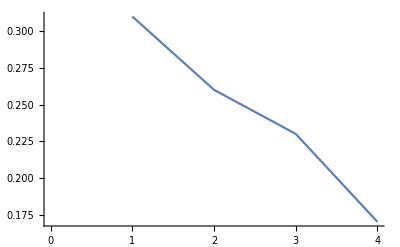

```mathematica
ListLinePlot[LC4]
```

iteration 5

```mathematica
w05=w04-Eps *G0[w04]
```

-7.93238

```mathematica
w15=w14-Eps*G1[w04,w14,2]
```

1.10193

```mathematica
w25=w24-Eps*G2[w04,w14,w24,2,2]
```

1.06903

```mathematica
FY5[x_]:=-(w15*x+w05)/w25
```

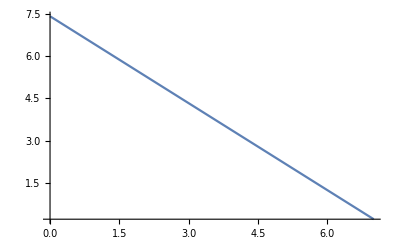

```mathematica
PY5=Plot[FY5[x],{x,0,7},PlotRange->All]
```

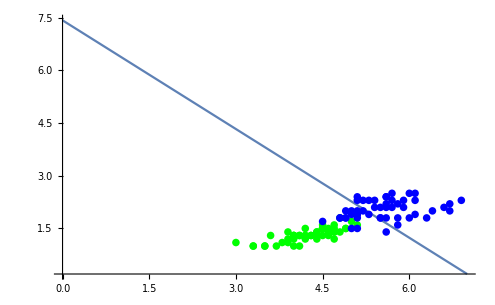

```mathematica
Show[PY5,class2,class3,PlotRange->All]
```

```mathematica
FFY5[{x1_,x2_}]:=If[FY5[x1]<x2,1,0]
```

```mathematica
MSE7=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY5[H[[n]]])^2
```

3/20

```mathematica
LC5={MSE3,MSE4,MSE5,MSE6,MSE7};
```

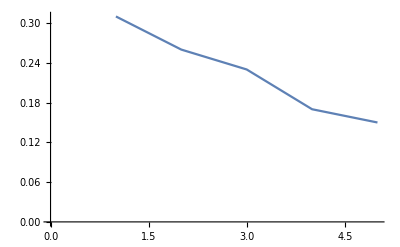

```mathematica
ListLinePlot[LC5]
```

iteration 6

```mathematica
w06=w05-Eps *G0[w05]
```

-7.91892

```mathematica
w16=w15-Eps*G1[w05,w15,2]
```

1.1218

```mathematica
w26=w25-Eps*G2[w05,w15,w25,2,2]
```

1.08206

```mathematica
FY6[x_]:=-(w16*x+w06)/w26
```

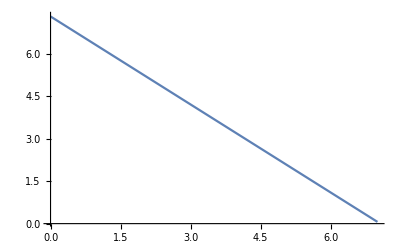

```mathematica
PY6=Plot[FY6[x],{x,0,7},PlotRange->All]
```

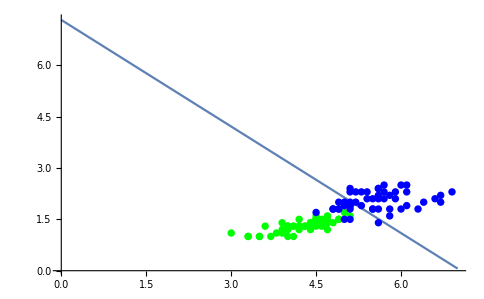

```mathematica
Show[PY6,class2,class3,PlotRange->All]
```

```mathematica
FFY6[{x1_,x2_}]:=If[FY6[x1]<x2,1,0]
```

```mathematica
MSE8=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY6[H[[n]]])^2
```

13/100

```mathematica
LC6={MSE3,MSE4,MSE5,MSE6,MSE7,MSE8};
```

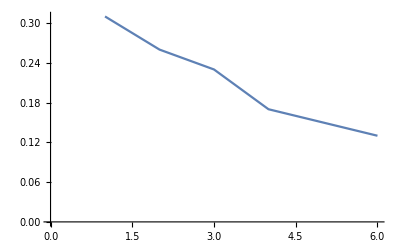

```mathematica
ListLinePlot[LC6]
```

iteration 7

```mathematica
w07=w06-Eps *G0[w06]
```

-7.90548

```mathematica
w17=w16-Eps*G1[w06,w16,2]
```

1.14149

```mathematica
w27=w26-Eps*G2[w06,w16,w26,2,2]
```

1.09483

```mathematica
FY7[x_]:=-(w17*x+w07)/w27
```

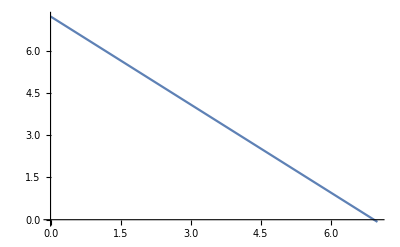

```mathematica
PY7=Plot[FY7[x],{x,0,7},PlotRange->All]
```

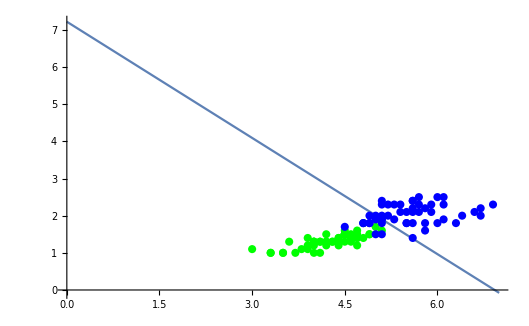

```mathematica
Show[PY7,class2,class3,PlotRange->All]
```

```mathematica
FFY7[{x1_,x2_}]:=If[FY7[x1]<x2,1,0]
```

```mathematica
MSE9=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY7[H[[n]]])^2
```

11/100

```mathematica
LC7={MSE3,MSE4,MSE5,MSE6,MSE7,MSE8,MSE9};
```

```mathematica
ListLinePlot[LC6]
```

-Graphics-

iteration 8

```mathematica
w08=w07-Eps *G0[w07]
```

-7.89206

```mathematica
w18=w17-Eps*G1[w07,w17,2]
```

1.16102

```mathematica
w28=w27-Eps*G2[w07,w17,w27,2,2]
```

1.10735

```mathematica
FY8[x_]:=-(w18*x+w08)/w28
```

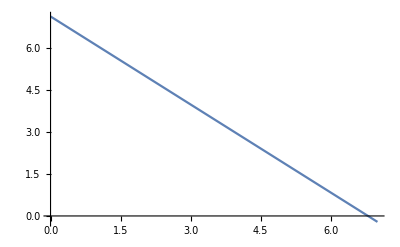

```mathematica
PY8=Plot[FY8[x],{x,0,7},PlotRange->All]
```

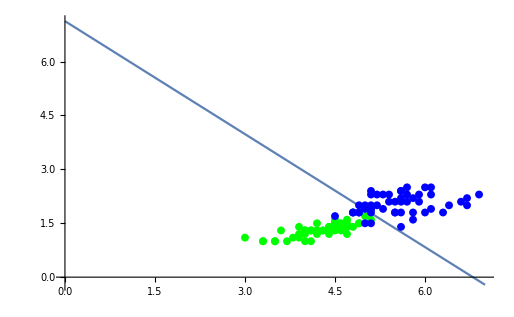

```mathematica
Show[PY8,class2,class3,PlotRange->All]
```

```mathematica
FFY8[{x1_,x2_}]:=If[FY8[x1]<x2,1,0]
```

```mathematica
MSE10=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY8[H[[n]]])^2
```

1/20

```mathematica
LC8={MSE3,MSE4,MSE5,MSE6,MSE7,MSE8,MSE9,MSE10};
```

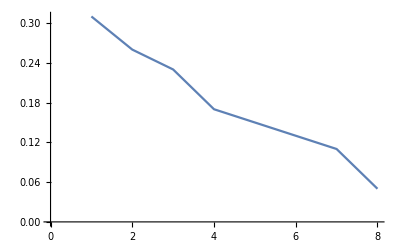

```mathematica
ListLinePlot[LC8]
```

iteration 9

```mathematica
w09=w08-Eps *G0[w08]
```

-7.87867

```mathematica
w19=w18-Eps*G1[w08,w18,2]
```

1.18038

```mathematica
w29=w28-Eps*G2[w08,w18,w28,2,2]
```

1.11962

```mathematica
FY9[x_]:=-(w19*x+w09)/w29
```

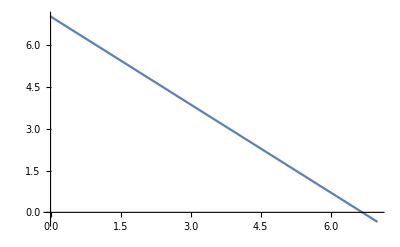

```mathematica
PY9=Plot[FY9[x],{x,0,7},PlotRange->All]
```

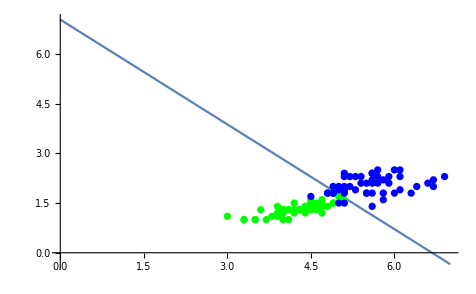

```mathematica
Show[PY9,class2,class3,PlotRange->All]
```

```mathematica
FFY9[{x1_,x2_}]:=If[FY9[x1]<x2,1,0]
```

```mathematica
MSE11=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY9[H[[n]]])^2
```

1/20

```mathematica
LC9={MSE3,MSE4,MSE5,MSE6,MSE7,MSE8,MSE9,MSE10,MSE11};
```

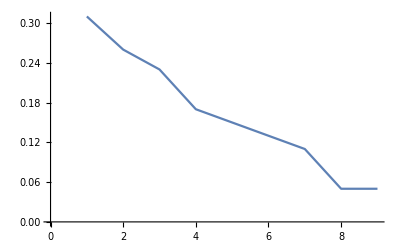

```mathematica
ListLinePlot[LC9]
```

iteration 10

```mathematica
w010=w09-Eps *G0[w09]
```

-7.86529

```mathematica
w110=w19-Eps*G1[w09,w19,2]
```

1.19958

```mathematica
w210=w29-Eps*G2[w09,w19,w29,2,2]
```

1.13165

```mathematica
FY10[x_]:=-(w110*x+w010)/w210
```

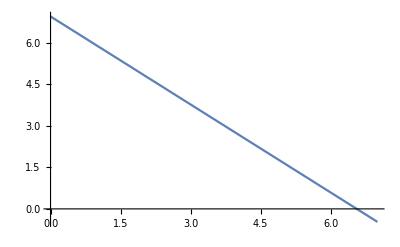

```mathematica
PY10=Plot[FY10[x],{x,0,7},PlotRange->All]
```

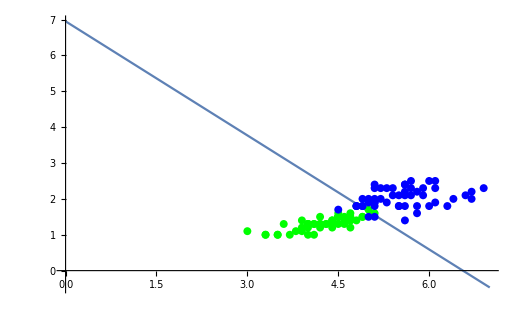

```mathematica
Show[PY10,class2,class3,PlotRange->All]
```

```mathematica
FFY10[{x1_,x2_}]:=If[FY10[x1]<x2,1,0]
```

```mathematica
MSE12=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY10[H[[n]]])^2
```

1/20

```mathematica
LC10={MSE3,MSE4,MSE5,MSE6,MSE7,MSE8,MSE9,MSE10,MSE11,MSE12};
```

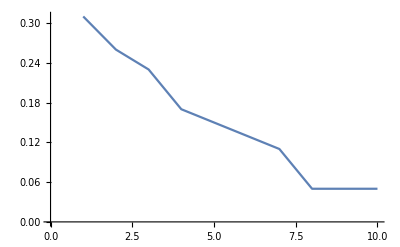

```mathematica
ListLinePlot[LC10]
```

iteration 11

```mathematica
w011=w010-Eps *G0[w010]
```

-7.85194

```mathematica
w111=w110-Eps*G1[w010,w110,2]
```

1.2186

```mathematica
w211=w210-Eps*G2[w010,w110,w210,2,2]
```

1.14343

```mathematica
FY11[x_]:=-(w111*x+w011)/w211
```

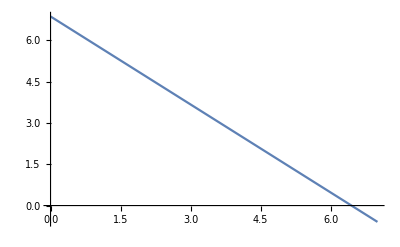

```mathematica
PY11=Plot[FY11[x],{x,0,7},PlotRange->All]
```

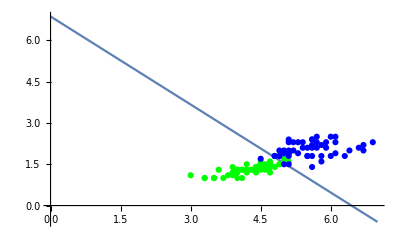

```mathematica
Show[PY11,class2,class3,PlotRange->All]
```

```mathematica
FFY11[{x1_,x2_}]:=If[FY11[x1]<x2,1,0]
```

```mathematica
MSE13=1/100*∑_(n=1)^100 (XXX1[H[[n]]]-FFY11[H[[n]]])^2
```

7/100

```mathematica
LC11={MSE3,MSE4,MSE5,MSE6,MSE7,MSE8,MSE9,MSE10,MSE11,MSE12,MSE13}
```

{31/100,13/50,23/100,17/100,3/20,13/100,11/100,1/20,1/20,1/20,7/100}

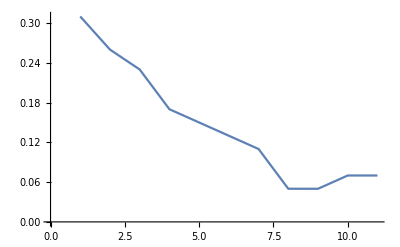

```mathematica
ListLinePlot[LC11]
```

d

If the step size is too small, learning will be slow; If the step size is too large, learning 
can oscillate between different sides of the minimum. After several tests, I chose the most appropriate one: 0.08/100.

e

When the learning curve gets very close to 0 and stop changing (mean square error also close to 0), the iteration should stop.

Exercise 4. Extra credit: Using a deep learning toolbox

a

Petal length and petal width of class 1

```mathematica
PL3={1.4,1.4,1.3,1.5,1.4,1.7,1.4,1.5,1.4,1.5,1.5,1.6,1.4,1.1,1.2,1.5,1.3,1.4,1.7,1.5,1.7,1.5,1,1.7,1.9,1.6,1.6,1.5,1.4,1.6,1.6,1.5,1.5,1.4,1.5,1.2,1.3,1.5,1.3,1.5,1.3,1.3,1.3,1.6,1.9,1.4,1.6,1.4,1.5,1.4};
Length[PL3]
```

50

```mathematica
PW3={0.2,0.2,0.2,0.2,0.2,0.4,0.3,0.2,0.2,0.1,0.2,0.2,0.1,0.1,0.2,0.4,0.4,0.3,0.3,0.3,0.2,0.4,0.2,0.5,0.2,0.2,0.4,0.2,0.2,0.2,0.2,0.4,0.1,0.2,0.1,0.2,0.2,0.1,0.2,0.2,0.3,0.3,0.2,0.6,0.4,0.3,0.2,0.2,0.2,0.2};
```

```mathematica
Length[PW3]
```

50

```mathematica
D3=Transpose@{PL3,PW3}
```

{{1.4,0.2},{1.4,0.2},{1.3,0.2},{1.5,0.2},{1.4,0.2},{1.7,0.4},{1.4,0.3},{1.5,0.2},{1.4,0.2},{1.5,0.1},{1.5,0.2},{1.6,0.2},{1.4,0.1},{1.1,0.1},{1.2,0.2},{1.5,0.4},{1.3,0.4},{1.4,0.3},{1.7,0.3},{1.5,0.3},{1.7,0.2},{1.5,0.4},{1,0.2},{1.7,0.5},{1.9,0.2},{1.6,0.2},{1.6,0.4},{1.5,0.2},{1.4,0.2},{1.6,0.2},{1.6,0.2},{1.5,0.4},{1.5,0.1},{1.4,0.2},{1.5,0.1},{1.2,0.2},{1.3,0.2},{1.5,0.1},{1.3,0.2},{1.5,0.2},{1.3,0.3},{1.3,0.3},{1.3,0.2},{1.6,0.6},{1.9,0.4},{1.4,0.3},{1.6,0.2},{1.4,0.2},{1.5,0.2},{1.4,0.2}}

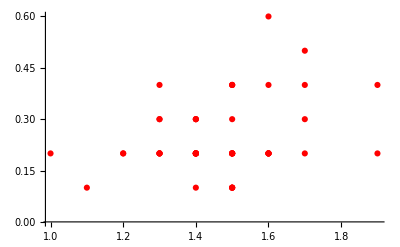

```mathematica
class1=ListPlot[D3,PlotStyle->Red]
```

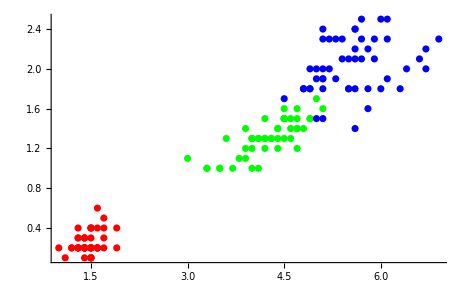

```mathematica
Show[class1,class2,class3,PlotRange->All]
```

sepal length and sepal width of all three classes

```mathematica
SL3={5.1,4.9,4.7,4.6,5,5.4,4.6,5,4.4,4.9,5.4,4.8,4.8,4.3,5.8,5.7,5.4,5.1,5.7,5.1,5.4,5.1,4.6,5.1,4.8,5,5,5.2,5.2,4.7,4.8,5.4,5.2,5.5,4.9,5,5.5,4.9,4.4,5.1,5,4.5,4.4,5,5.1,4.8,5.1,4.6,5.3,5};

SL1={7,6.4,6.9,5.5,6.5,5.7,6.3,4.9,6.6,5.2,5,5.9,6,6.1,5.6,6.7,5.6,5.8,6.2,5.6,5.9,6.1,6.3,6.1,6.4,6.6,6.8,6.7,6,5.7,5.5,5.5,5.8,6,5.4,6,6.7,6.3,5.6,5.5,5.5,6.1,5.8,5,5.6,5.7,5.7,6.2,5.1,5.7};

SL2={6.3,5.8,7.1,6.3,6.5,7.6,4.9,7.3,6.7,7.2,6.5,6.4,6.8,5.7,5.8,6.4,6.5,7.7,7.7,6,6.9,5.6,7.7,6.3,6.7,7.2,6.2,6.1,6.4,7.2,7.4,7.9,6.4,6.3,6.1,7.7,6.3,6.4,6,6.9,6.7,6.9,5.8,6.8,6.7,6.7,6.3,6.5,6.2,5.9};
```

```mathematica
Length[SL3]
```

50

```mathematica
Length[SL2]
```

50

```mathematica
Length[SL1]
```

50

```mathematica
SW3={3.5,3,3.2,3.1,3.6,3.9,3.4,3.4,2.9,3.1,3.7,3.4,3,3,4,4.4,3.9,3.5,3.8,3.8,3.4,3.7,3.6,3.3,3.4,3,3.4,3.5,3.4,3.2,3.1,3.4,4.1,4.2,3.1,3.2,3.5,3.1,3,3.4,3.5,2.3,3.2,3.5,3.8,3,3.8,3.2,3.7,3.3};

SW1={3.2,3.2,3.1,2.3,2.8,2.8,3.3,2.4,2.9,2.7,2,3,2.2,2.9,2.9,3.1,3,2.7,2.2,2.5,3.2,2.8,2.5,2.8,2.9,3,2.8,3,2.9,2.6,2.4,2.4,2.7,2.7,3,3.4,3.1,2.3,3,2.5,2.6,3,2.6,2.3,2.7,3,2.9,2.9,2.5,2.8};

SW2={3.3,2.7,3,2.9,3,3,2.5,2.9,2.5,3.6,3.2,2.7,3,2.5,2.8,3.2,3,3.8,2.6,2.2,3.2,2.8,2.8,2.7,3.3,3.2,2.8,3,2.8,3,2.8,3.8,2.8,2.8,2.6,3,3.4,3.1,3,3.1,3.1,3.1,2.7,3.2,3.3,3,2.5,3,3.4,3};
```

```mathematica
Length[SW3]
```

50

```mathematica
Length[SW2]
```

50

```mathematica
Length[SW1]
```

50

b

```mathematica
DD1=Transpose@{SL3,SW3,PL3,PW3}
```

{{5.1,3.5,1.4,0.2},{4.9,3,1.4,0.2},{4.7,3.2,1.3,0.2},{4.6,3.1,1.5,0.2},{5,3.6,1.4,0.2},{5.4,3.9,1.7,0.4},{4.6,3.4,1.4,0.3},{5,3.4,1.5,0.2},{4.4,2.9,1.4,0.2},{4.9,3.1,1.5,0.1},{5.4,3.7,1.5,0.2},{4.8,3.4,1.6,0.2},{4.8,3,1.4,0.1},{4.3,3,1.1,0.1},{5.8,4,1.2,0.2},{5.7,4.4,1.5,0.4},{5.4,3.9,1.3,0.4},{5.1,3.5,1.4,0.3},{5.7,3.8,1.7,0.3},{5.1,3.8,1.5,0.3},{5.4,3.4,1.7,0.2},{5.1,3.7,1.5,0.4},{4.6,3.6,1,0.2},{5.1,3.3,1.7,0.5},{4.8,3.4,1.9,0.2},{5,3,1.6,0.2},{5,3.4,1.6,0.4},{5.2,3.5,1.5,0.2},{5.2,3.4,1.4,0.2},{4.7,3.2,1.6,0.2},{4.8,3.1,1.6,0.2},{5.4,3.4,1.5,0.4},{5.2,4.1,1.5,0.1},{5.5,4.2,1.4,0.2},{4.9,3.1,1.5,0.1},{5,3.2,1.2,0.2},{5.5,3.5,1.3,0.2},{4.9,3.1,1.5,0.1},{4.4,3,1.3,0.2},{5.1,3.4,1.5,0.2},{5,3.5,1.3,0.3},{4.5,2.3,1.3,0.3},{4.4,3.2,1.3,0.2},{5,3.5,1.6,0.6},{5.1,3.8,1.9,0.4},{4.8,3,1.4,0.3},{5.1,3.8,1.6,0.2},{4.6,3.2,1.4,0.2},{5.3,3.7,1.5,0.2},{5,3.3,1.4,0.2}}

```mathematica
DD2=Transpose@{SL1,SW1,PL1,PW1}
```

{{7,3.2,4.7,1.4},{6.4,3.2,4.5,1.5},{6.9,3.1,4.9,1.5},{5.5,2.3,4,1.3},{6.5,2.8,4.6,1.5},{5.7,2.8,4.5,1.3},{6.3,3.3,4.7,1.6},{4.9,2.4,3.3,1},{6.6,2.9,4.6,1.3},{5.2,2.7,3.9,1.4},{5,2,3.5,1},{5.9,3,4.2,1.5},{6,2.2,4,1},{6.1,2.9,4.7,1.4},{5.6,2.9,3.6,1.3},{6.7,3.1,4.4,1.4},{5.6,3,4.5,1.5},{5.8,2.7,4.1,1},{6.2,2.2,4.5,1.5},{5.6,2.5,3.9,1.1},{5.9,3.2,4.8,1.8},{6.1,2.8,4,1.3},{6.3,2.5,4.9,1.5},{6.1,2.8,4.7,1.2},{6.4,2.9,4.3,1.3},{6.6,3,4.4,1.4},{6.8,2.8,4.8,1.4},{6.7,3,5,1.7},{6,2.9,4.5,1.5},{5.7,2.6,3.5,1},{5.5,2.4,3.8,1.1},{5.5,2.4,3.7,1},{5.8,2.7,3.9,1.2},{6,2.7,5.1,1.6},{5.4,3,4.5,1.5},{6,3.4,4.5,1.6},{6.7,3.1,4.7,1.5},{6.3,2.3,4.4,1.3},{5.6,3,4.1,1.3},{5.5,2.5,4,1.3},{5.5,2.6,4.4,1.2},{6.1,3,4.6,1.4},{5.8,2.6,4,1.2},{5,2.3,3.3,1},{5.6,2.7,4.2,1.3},{5.7,3,4.2,1.2},{5.7,2.9,4.2,1.3},{6.2,2.9,4.3,1.3},{5.1,2.5,3,1.1},{5.7,2.8,4.1,1.3}}

```mathematica
DD3=Transpose@{SL2,SW2,PL2,PW2}
```

{{6.3,3.3,6,2.5},{5.8,2.7,5.1,1.9},{7.1,3,5.9,2.1},{6.3,2.9,5.6,1.8},{6.5,3,5.8,2.2},{7.6,3,6.6,2.1},{4.9,2.5,4.5,1.7},{7.3,2.9,6.3,1.8},{6.7,2.5,5.8,1.8},{7.2,3.6,6.1,2.5},{6.5,3.2,5.1,2},{6.4,2.7,5.3,1.9},{6.8,3,5.5,2.1},{5.7,2.5,5,2},{5.8,2.8,5.1,2.4},{6.4,3.2,5.3,2.3},{6.5,3,5.5,1.8},{7.7,3.8,6.7,2.2},{7.7,2.6,6.9,2.3},{6,2.2,5,1.5},{6.9,3.2,5.7,2.3},{5.6,2.8,4.9,2},{7.7,2.8,6.7,2},{6.3,2.7,4.9,1.8},{6.7,3.3,5.7,2.1},{7.2,3.2,6,1.8},{6.2,2.8,4.8,1.8},{6.1,3,4.9,1.8},{6.4,2.8,5.6,2.1},{7.2,3,5.8,1.6},{7.4,2.8,6.1,1.9},{7.9,3.8,6.4,2},{6.4,2.8,5.6,2.2},{6.3,2.8,5.1,1.5},{6.1,2.6,5.6,1.4},{7.7,3,6.1,2.3},{6.3,3.4,5.6,2.4},{6.4,3.1,5.5,1.8},{6,3,4.8,1.8},{6.9,3.1,5.4,2.1},{6.7,3.1,5.6,2.4},{6.9,3.1,5.1,2.3},{5.8,2.7,5.1,1.9},{6.8,3.2,5.9,2.3},{6.7,3.3,5.7,2.5},{6.7,3,5.2,2.3},{6.3,2.5,5,1.9},{6.5,3,5.2,2},{6.2,3.4,5.4,2.3},{5.9,3,5.1,1.8}}

Training: 0 for class 1, 1 for class 2, 2 for class 3

```mathematica
cc=Classify[<|0->DD1,1->DD2,2->DD3|>,Method->"LogisticRegression"];
```

example output:

```mathematica
cc[{6.4,2.7,5.3,1.9}]
```

2

```mathematica
cc[DD1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

function that calculate incorrect classifications for class 1

```mathematica
∑_(i=1)^50 If[cc[DD1][[i]]≠0,1,0]
```

0

Correct classifications for class 1: 50 / 50

```mathematica
cc[DD2]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

function that calculate incorrect classifications for class 2

```mathematica
∑_(i=1)^50 If[cc[DD2][[i]]≠1,1,0]
```

1

Correct classifications for class 2: 49 / 50

```mathematica
cc[DD3]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

function that calculate incorrect classifications for class 3

```mathematica
∑_(i=1)^50 If[cc[DD3][[i]]≠2,1,0]
```

1

Correct classifications for class 3: 49 / 50

Total correct classifications : 148 / 150

Methods used below are from Wolfram: Tutorial to “Training on large datasets”

```mathematica
trainingData=ExampleData[{"MachineLearning","FisherIris"},"TrainingData"];
testData=ExampleData[{"MachineLearning","FisherIris"},"TestData"];
```

```mathematica
RandomSample[trainingData,5]
```

{{5.,2.3,3.3,1.}→versicolor,{5.4,3.9,1.7,0.4}→setosa,{6.5,2.8,4.6,1.5}→versicolor,{6.7,3.3,5.7,2.1}→virginica,{4.8,3.4,1.6,0.2}→setosa}

```mathematica
Needs["MongoLink`"]
```

```mathematica
client=MongoConnect[]
```

MongoClient[…]

```mathematica
collection=MongoGetCollection[client,"WolframNNTutorialDatabase","WolframNNTutorialCollection"]
```

MongoCollection[…]

```mathematica
trainingDataDoc=<|"Input"->First[#],"Output"->Last[#]|>&/@trainingData;
```

```mathematica
RandomSample[trainingDataDoc,2]
```

{<|Input→{6.7,3.1,4.4,1.4},Output→versicolor|>,<|Input→{6.7,3.,5.2,2.3},Output→virginica|>}

```mathematica
MongoCollectionInsert[collection,trainingDataDoc]
```

MongoCollectionInsert::mongoliberr: C Function WL_BulkOpExecute failed. Error from Mongo C Driver: "No suitable servers found (`serverSelectionTryOnce` set): [connection refused calling ismaster on 'localhost:27017']"

$Failed

```mathematica
labels=MongoCollectionDistinct[collection,"Output"]
```

MongoCollectionDistinct::mongoliberr: C Function WL_MongoCollectionCommandSimple failed. Error from Mongo C Driver: "No suitable servers found (`serverSelectionTryOnce` set): [connection refused calling ismaster on 'localhost:27017']"

$Failed

```mathematica
net=NetChain[{3,SoftmaxLayer[]},"Input"->4,"Output"->NetDecoder[{"Class",labels}]]
```

NetDecoder::netinvparam: Value given for the labels (first argument) should be either Automatic or a list of expressions, but was $Failed instead.

NetChain::invportshape: Specification $Failed is not compatible with port "Output", which must be a tensor.

$Failed

```mathematica
ReadList@MongoCollectionAggregate[collection,{<|"$project"-><|"_id"->False|>|>,<|"$sample"-><|"size"->2|>|>}]
```

{}

```mathematica
gen1=Function[ReadList@MongoCollectionAggregate[collection,{<|"$project"-><|"_id"->False|>|>,<|"$sample"-><|"size"->#BatchSize|>|>}]];
```

```mathematica
gen2=Function[First@ReadList@MongoCollectionAggregate[collection,{<|"$sample"-><|"size"->#BatchSize|>|>,<|"$group"-><|"_id"->Null,"Input"-><|"$push"->"$Input"|>,"Output"-><|"$push"->"$Output"|>|>|>,<|"$project"-><|"_id"->False|>|>}]];
```

```mathematica
trained=NetTrain[net,gen2,BatchSize->64,ValidationSet->testData]
```

NetTrain::invnet: First argument to NetTrain should be a fully specified net.

$Failed

```mathematica
roundSize=MongoCollectionCount[collection]
```

MongoCollectionCount::mongoliberr: C Function WL_MongoCollectionCount failed. Error from Mongo C Driver: "No suitable servers found (`serverSelectionTryOnce` set): [connection refused calling ismaster on 'localhost:27017']"

$Failed

train the net for 2000 rounds

```mathematica
trained=NetTrain[net,{gen2,"RoundLength"->roundSize},BatchSize->64,ValidationSet->testData,MaxTrainingRounds->2000]
```

NetTrain::invnet: First argument to NetTrain should be a fully specified net.

$Failed

```mathematica
cm=ClassifierMeasurements[trained,testData];
```

ClassifierMeasurements::wrgfunc: The first argument should be a ClassifierFunction instead of $Failed.

```mathematica
cm["Accuracy"] == 1
```

ClassifierMeasurements[$Failed,{{5.1,3.5,1.4,0.2}→setosa,{4.9,3.,1.4,0.2}→setosa,{4.6,3.4,1.4,0.3}→setosa,{4.4,2.9,1.4,0.2}→setosa,{4.3,3.,1.1,0.1}→setosa,{5.8,4.,1.2,0.2}→setosa,{5.1,3.5,1.4,0.3}→setosa,{5.7,3.8,1.7,0.3}→setosa,{5.1,3.8,1.5,0.3}→setosa,{5.2,3.4,1.4,0.2}→setosa,{5.5,4.2,1.4,0.2}→setosa,{5.1,3.4,1.5,0.2}→setosa,{4.5,2.3,1.3,0.3}→setosa,{4.8,3.,1.4,0.3}→setosa,{5.1,3.8,1.6,0.2}→setosa,{5.7,2.8,4.5,1.3}→versicolor,{5.,2.,3.5,1.}→versicolor,{6.1,2.9,4.7,1.4}→versicolor,{5.6,2.9,3.6,1.3}→versicolor,{5.8,2.7,4.1,1.}→versicolor,{6.2,2.2,4.5,1.5}→versicolor,{5.9,3.2,4.8,1.8}→versicolor,{6.1,2.8,4.,1.3}→versicolor,{6.4,2.9,4.3,1.3}→versicolor,{6.,2.9,4.5,1.5}→versicolor,{5.4,3.,4.5,1.5}→versicolor,{6.,3.4,4.5,1.6}→versicolor,{5.6,2.7,4.2,1.3}→versicolor,{5.7,3.,4.2,1.2}→versicolor,{6.2,2.9,4.3,1.3}→versicolor,{6.3,3.3,6.,2.5}→virginica,{7.1,3.,5.9,2.1}→virginica,{6.5,3.,5.8,2.2}→virginica,{7.6,3.,6.6,2.1}→virginica,{6.4,3.2,5.3,2.3}→virginica,{7.7,3.8,6.7,2.2}→virginica,{6.9,3.2,5.7,2.3}→virginica,{7.2,3.2,6.,1.8}→virginica,{6.4,2.8,5.6,2.1}→virginica,{7.2,3.,5.8,1.6}→virginica,{7.4,2.8,6.1,1.9}→virginica,{7.9,3.8,6.4,2.}→virginica,{6.4,2.8,5.6,2.2}→virginica,{6.3,3.4,5.6,2.4}→virginica,{6.7,3.3,5.7,2.5}→virginica}][Accuracy]==1